```mathematica
E0[h_,m_,k_]:=(h^2 k^2)/(2m)
```

```mathematica
thing[h_,m_,k_,K_,U_]:= (E0[h,m,k]+E0[h,m,k-K])/2+Sqrt[((E0[h,m,k]-E0[h,m,k-K])/2)^2+U^2]
```

```mathematica
thing2[h_,m_,k_,K_,U_]:= (E0[h,m,k]+E0[h,m,k-K])/2-Sqrt[((E0[h,m,k]-E0[h,m,k-K])/2)^2+U^2]
```

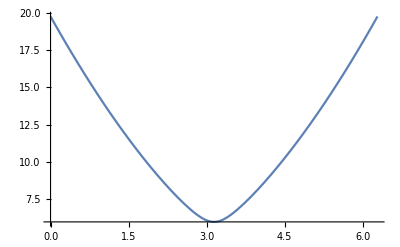

```mathematica
Plot[thing[1,1,k,2Pi,1],{k,0,2Pi}]
```

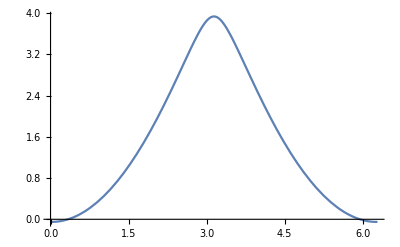

```mathematica
Plot[thing2[1,1,k,2Pi,1],{k,0,2Pi}]
```

```mathematica
max=100*FindMinimum[thing[1,1,k,1,0.01],{k,0.5}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{13.5,{100 (k→0.5)}}

```mathematica
min=100*FindMaximum[thing2[1,1,k,1,0.01],{k,0.5}]
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{11.5,{100 (k→0.5)}}

```mathematica
Plot[{thing[10,1,k,1,1],thing2[10,1,k,1,1]},{k,0,0.5},PlotRange->{0,30},BoxRatios{1,2}]
```

Plot::nonopt: Options expected (instead of BoxRatios {1,2}) beyond position 2 in Plot[{thing[10,1,k,1,1],thing2[10,1,k,1,1]},{k,0,0.5},PlotRange→{0,30},BoxRatios {1,2}]. An option must be a rule or a list of rules.

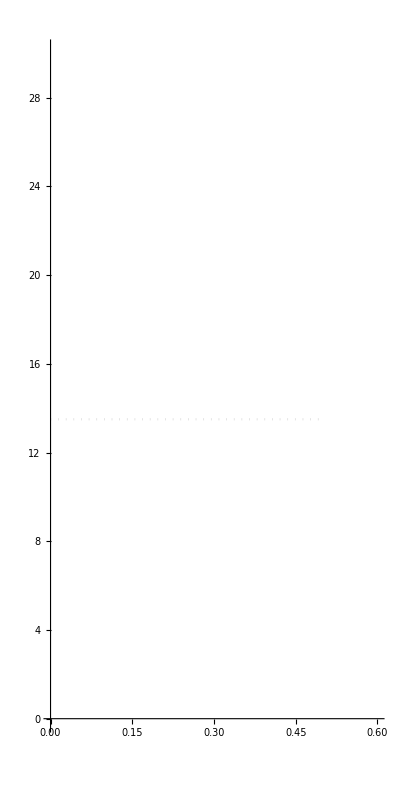

```mathematica
lines=Plot[max,{k,0,0.5},PlotRange->{{0,0.6},{0,30}},AspectRatio->2,PlotStyle->{{Dotted,LightGray}}]
```

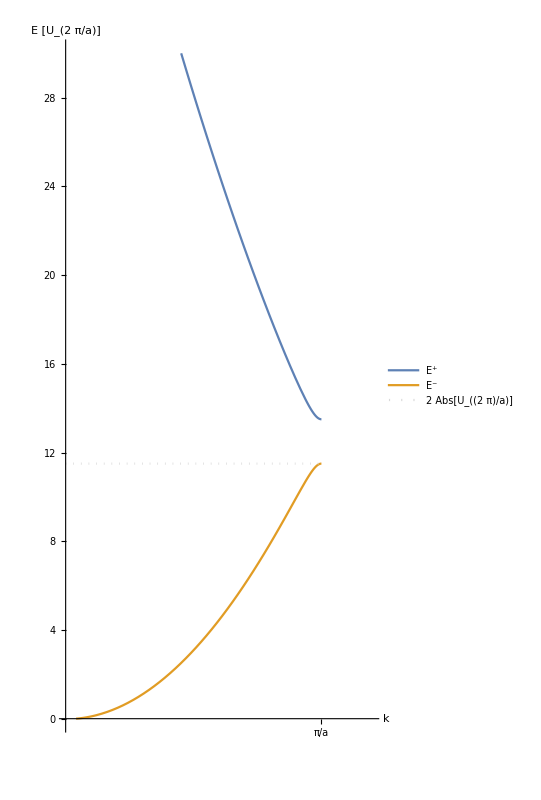

```mathematica
curves=Plot[{100*thing[1,1,k,1,0.01],100*thing2[1,1,k,1,0.01],min},{k,0,0.5},PlotRange->{{0,0.6},{0,30}},PlotStyle->{Automatic,Automatic,{Dotted,LightGray}},AspectRatio->2,AxesLabel->{"k","E   [U_(2  π/a)]"},PlotLegends->{"E^+","E^-",2Abs[Subscript[U, 2π/a]]},Ticks->{{{0.5,π/a}},Automatic}]
```

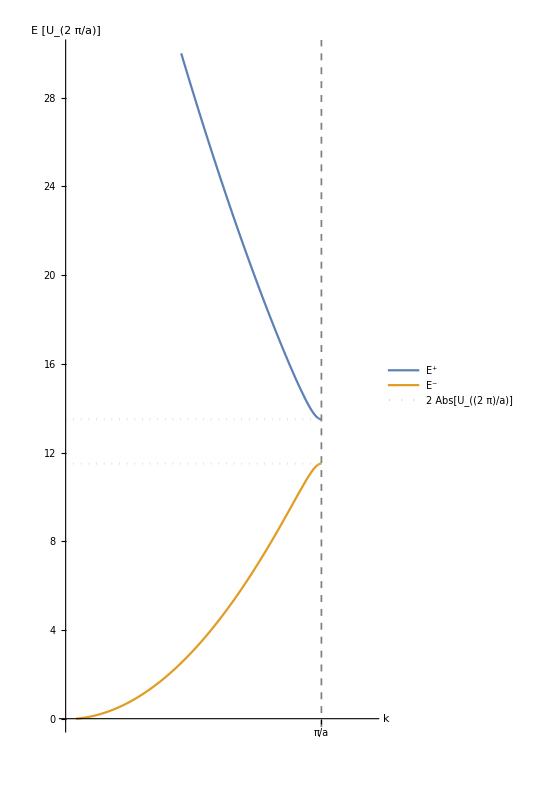

```mathematica
Show[curves,lines,Epilog->{Gray,Dashed,AbsoluteThickness[1.25],Line[{{0.5,-1},{0.5,31}}]}]
```

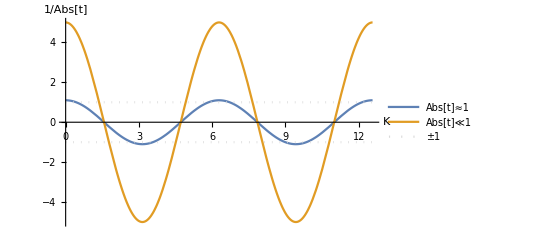

```mathematica
Plot[{1.1*Cos[Ka],5*Cos[Ka],1,-1},{Ka,0,4Pi},PlotStyle->{Automatic,Automatic,{Dotted,LightGray},{Dotted,LightGray}},PlotLegends->{Abs[t]≈1,Abs[t]≪1,±1},Ticks->{None,None},AxesLabel->{K,1/Abs[t]}]
```

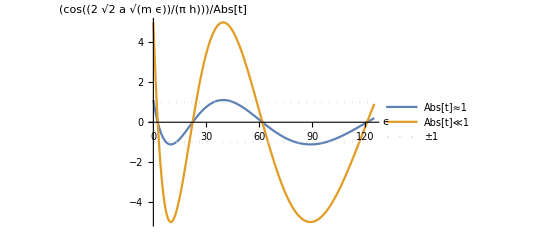

```mathematica
Plot[{Cos[Sqrt[x]]/.9,5*Cos[Sqrt[x]],1,-1},{x,0,125},PlotStyle->{Automatic,Automatic,{Dotted,LightGray},{Dotted,LightGray}},PlotLegends->{Abs[t]≈1,Abs[t]≪1,±1},Ticks->{None,None},AxesLabel->{ϵ,Cos[(a Sqrt[2m ϵ])/(h/2Pi)]/Abs[t]}]
```